# Versuch 49

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15]}
```

{Frame→True,Axes→False,FrameStyle→Directive[GrayLevel[0],Thickness[0.003]],ImageSize→700,FrameTicksStyle→Directive[GrayLevel[0],15]}

## Data

```mathematica
rawData=Import[NotebookDirectory[]<>"Messung Franck-Hertz-Kurve für Neon 1.txt"];
```

```mathematica
(*rawData=Import[NotebookDirectory[]<>"Messung Franck-Hertz-Kurve für Quecksilber 2.txt"];*)
```

```mathematica
data=Map[StringReplace[","->"."],StringSplit[StringSplit[rawData,"\n"],"	"]][[2;;]];
```

```mathematica
data=Map[ToExpression,data,{2}];
```

```mathematica
cleanedData=DeleteAnomalies[data[[All,{2,3}]],AcceptanceThreshold->0.3];
```

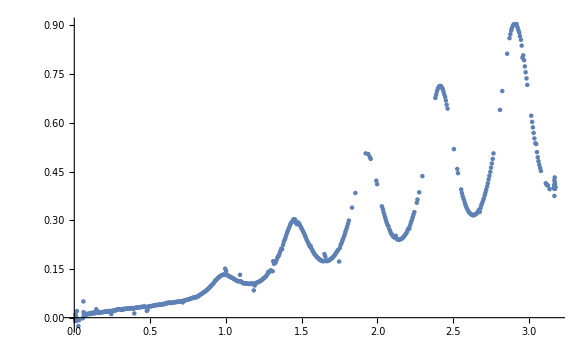

```mathematica
ListPlot[cleanedData]
```

```mathematica
dataProcessed=data[[All,{2,3}]];
```

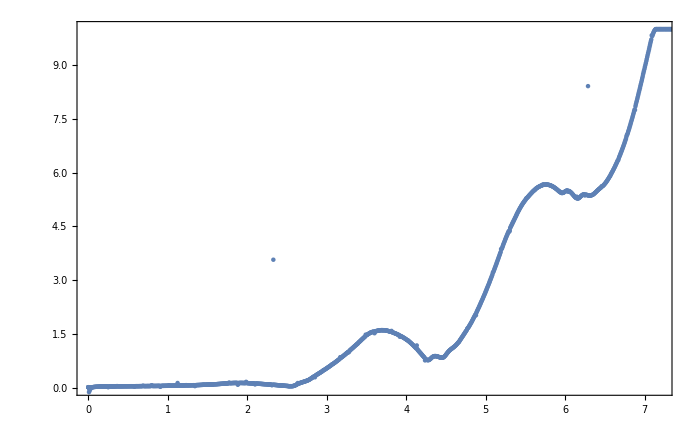

```mathematica
ListPlot[dataProcessed,PlotRange->{{0,7.2},{0,10}},pltsettings]
```

```mathematica
intervals={{1.7,2.1},{3.5,3.8},{4.24,4.44},{5.65,5.85},{5.97,6.15},{6.15,6.286}};
```

```mathematica
MaximalBy[{{1,2},{3,4}},Last]
```

{{3,4}}

```mathematica
findPosition[int_]:=MaximalBy[DeleteCases[dataProcessed,x_/;x[[1]]<=int[[1]]||x[[1]]>int[[2]]],Last][[1,1]]
```

```mathematica
maxPositions=findPosition/@intervals
```

{1.984,3.698,4.358,5.72,6.03,6.236}

```mathematica
colors={Red,Red,Blue,Red,Blue,Blue};
```

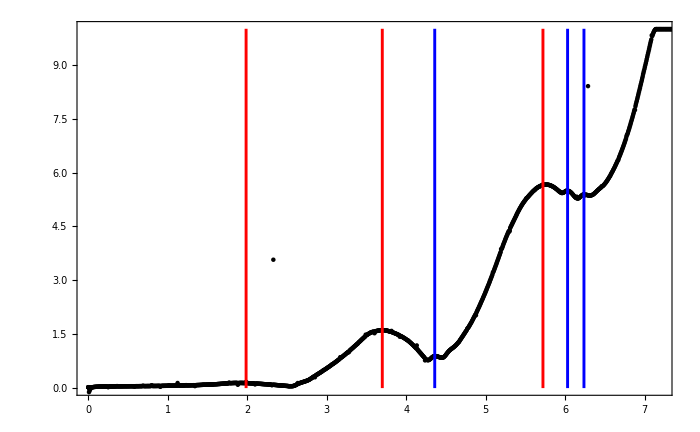

```mathematica
Show[ListPlot[dataProcessed,PlotRange->{{0,7.2},{0,10}},PlotStyle->Black,pltsettings],Graphics[Join@@Table[{Thickness[0.003],colors[[i]],Line[{{maxPositions[[i]],0},{maxPositions[[i]],10}}]},{i,1,Length[maxPositions]}]]]
```

```mathematica
Export[NotebookDirectory[]<>"fig9.pdf",Show[ListPlot[dataProcessed,PlotRange->{{0,7.2},{0,10}},PlotStyle->Black,pltsettings],Graphics[Join@@Table[{Thickness[0.003],colors[[i]],Line[{{maxPositions[[i]],0},{maxPositions[[i]],10}}]},{i,1,Length[maxPositions]}]]],Background->None];
```